```mathematica
delta=2 9^2/(2 2.1 10^8 0.1 0.2) 
delta 2.1 10^8 0.1 0.2/9
```

0.0000192857

9.

```mathematica
Integrate[xx^2,{xx,0,2.}]
```

2.66667

```mathematica
dll=0;
Ls=0;
steps=10000;
dx=2/steps;
y=0.;
x=0.;
For[i=1,i<=steps,i++,
y+=dx((x)^2 +(x+dx)^2)/2;
x+=dx;

]
y
```

2.66667

```mathematica
steps=1000;
dx=9/steps;
y=0.;
x=0.;
fx[x_]:=2 x;
For[i=1,i<=steps,i++,
y+=(fx[x]+fx[x+dx])dx/2;
x+=dx;

]
y/(2.1 10^8 0.1 0.2)
```

0.0000192857

```mathematica
steps=1000;
dx=9/steps;
y=0.;
x=0.;
w=2;
For[i=1,i<=steps,i++,
y+=((w x)+(w (x+dx)))dx/2;
x+=dx;

]
y/(2.1 10^8 0.1 0.2)
```

0.0000192857

```mathematica
steps=1000;
dx=9/steps;
y=0.;
x=0.;
w=3;
e=2.1 10^8;
a=0.1 0.2;
For[i=1,i<=steps,i++,
y+=w(2 x dx+dx^2)/2;
x+=dx;
]
y/(e a)
```

0.0000289286

```mathematica
ComputeAxialReaction[Force_,area_,L_,w_]:=Block[{tabf,df,Steps=100,DL,DF,young = 2.1 10^8,dx,x},
dx=L/Steps;
DL=0.;
x=0.;
For[i=1,i≤Steps,i++,
DL+=w(2 x dx+dx^2)/2;
x+=dx;
];
DL=DL/(young area);
Print["DL = ",DL];
DF=young DL/L  area
];
R=0;
w=3;
stepss=10;
dx=9/stepss;
f=0;
x=0.;
area=0.1 0.2;
For[jj=1,jj≤stepss,jj++,
R+=ComputeAxialReaction[f,area,dx,w];
f=x w;
x+=dx;
Print[x];
];
```

DL = 2.89286×10^-7

0.9

DL = 2.89286×10^-7

1.8

DL = 2.89286×10^-7

2.7

DL = 2.89286×10^-7

3.6

DL = 2.89286×10^-7

4.5

DL = 2.89286×10^-7

5.4

DL = 2.89286×10^-7

6.3

DL = 2.89286×10^-7

7.2

DL = 2.89286×10^-7

8.1

DL = 2.89286×10^-7

9.

```mathematica
x
```

0.9

```mathematica
R
```

13.5

```mathematica
dx
```

9/10

```mathematica
x
```

0.9

```mathematica
Clear[L]
Integrate[P/2 X X/2,{X,0,L/2}]+Integrate[P/2 (L-X) 1/2 (L-X),{X,L/2,L}]
```

(L^3 P)/48

```mathematica
-P/4((6 L^3 - 3 L^3+2 L^3)/12)+P L^3/12+P L^3/96
```

-(L^3 P)/96

```mathematica
(Integrate[P/2 X X/2,X]/.X->L/2 )-Integrate[P/2 (L-X) 1/2 (L-X),X]/.X->L/2//Simplify
```

(L^3 P)/48

```mathematica
Integrate[P/2 (L-X) 1/2 (L-X),X]/.X->L/2
```

-(L^3 P)/96

```mathematica
Integrate[P/2 (L-X) 1/2 (L-X),X]
```

-1/12 P (L-X)^3

```mathematica
P/4Integrate[(L^2-2 L X+X^2),X]/.X->L
P/4Integrate[X X,X]/.X->L/2
-P/4Integrate[(L^2-2 L X+X^2),X]/.X->L/2
```

(L^3 P)/12

(L^3 P)/96

-(7 L^3 P)/96

```mathematica
96/6
```

16

```mathematica
-(7 L^3 P)/96+(L^3 P)/96
-(L^3 P)/16+(L^3 P)/12
```

-(L^3 P)/16

(L^3 P)/48

```mathematica
(P/4Integrate[X X,X]/.X->L/2)+(P/4Integrate[(L^2-2 L X+X^2),X]/.X->L)-(P/4Integrate[(L^2-2 L X+X^2),X]/.X->L/2)
```

(L^3 P)/48

```mathematica
(Integrate[(X/L)(M X/L),{X,0,L/2}]+Integrate[(X/L-M)(X/L-1),{X,L/2,L}]/.L->4/.M->1)/(2.1 10^8 (0.1 0.2^3)/12)
```

0.0000238095

```mathematica
(Integrate[(X/L)(M X/L),{X,0,L/2}]+Integrate[X X/L^2 - X  M/L - X/L+M,{X,L/2,L}]/.L->4/.M->1)/(2.1 10^8 (0.1 0.2^3)/12)
```

0.0000238095

```mathematica
Integrate[P/2 X X/2,{X,0,L/2}]
```

(L^3 P)/96

```mathematica
P/4 (7 L^3)/24-P/4 L^3/3
```

-(L^3 P)/96

```mathematica
P/4 Expand[ (L-X)  (L-X)]
```

1/4 P (L^2-2 L X+X^2)

```mathematica
Integrate[X X/L^2 - X  M/L - X/L+M,X]/.X->L/2//Simplify
```

1/24 L (-2+9 M)

```mathematica
Integrate[(X/L)(M X/L),{X,0,L/2}]+Integrate[X X/L^2 - X  M/L - X/L+M,{X,L/2,L}]
```

-L/12+(L M)/6

```mathematica
a=Integrate[M X/L,X]+C1
b=Integrate[a,X]
elasta=b/.C1->-(L M)/24//FullSimplify
a=Integrate[M X/L-M,X]+C1
b=Integrate[a,X]+C2
elastb=b/.C1->(-3 C2-L^2 M)/(3 L)/.C2->-(L^2 M)/8//FullSimplify
```

C1+(M X^2)/(2 L)

C1 X+(M X^3)/(6 L)

-(M X (L^2-4 X^2))/(24 L)

C1+M (-X+X^2/(2 L))

C2+C1 X-(M X^2)/2+(M X^3)/(6 L)

-(M (3 L^3+5 L^2 X+12 L X^2-4 X^3))/(24 L)

```mathematica
Solve[(b/.X->L/2/.C1->(-3 C2+L^2 M)/(3 L))==0,C2]
Solve[(b/.X->L)==0,C1]
```

{{C2→-(L^2 M)/8}}

{{C1→(-3 C2+L^2 M)/(3 L)}}

```mathematica
ptv=Integrate[(X/L)(M X/L),{X,0,L/2}]+Integrate[(X/L-M)(X/L-1),{X,L/2,L}]
```

-L/12+(L M)/6

```mathematica
Simplify[(D[elast,X]/.X->L/2)-(ptv)]
```

1/12 (L-L M)

```mathematica
elast
```

-(M X (L^2-4 X^2))/(24 L)

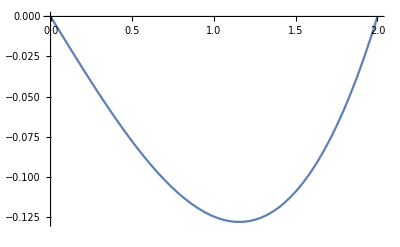

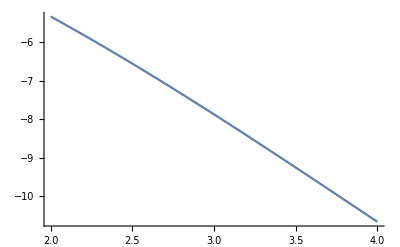

```mathematica
Plot[elasta/.L->4/.M->1,{X,0,2}]
Plot[elastb/.L->4/.M->1,{X,2,4}]
```

```mathematica
((elast/.X->L/2)/.L->4/.M->1)/(2.1 10^8 (0.1 0.2^3)/12)
((D[elast,X]/.X->L/2)/.L->4/.M->1)/(2.1 10^8 (0.1 0.2^3)/12)
```

0.

0.0000238095

```mathematica
Solve[(b/.X->L)==0,C1]
```

{{C1→-(L M)/3}}

```mathematica
D[elasta,X]
```

(M X^2)/(3 L)-(M (L^2-4 X^2))/(24 L)

```mathematica
D[elasta,X]/.X->L/2//Simplify
elasta/.X->L/2//Simplify
```

(L M)/12

0